```mathematica
Quit[]
```

```mathematica
LaunchKernels[8(*8*)];
Needs["TBMethod`"]
ParallelNeeds["TBMethod`"]
StringTemplate["TBMethod<*\"`\"*>`1`<*\"`\"*>*"]/@{"MDConstruct","EigenSpect","LGFF","DataVisualization"}
Scan[Echo@*Information][%]
```

{TBMethod`MDConstruct`*,TBMethod`EigenSpect`*,TBMethod`LGFF`*,TBMethod`DataVisualization`*}

### tFunc

```mathematica
Clear[tFunckm]
tFunckm[t_,λSO_,λR_,λv_][inf_->ptf_,ini_->pti_]:=Module[{vd=ptf-pti,d,x,y,fills,conds,zero=1.*^-5,,theta},
d=Norm[vd];{x,y}=Flatten[TakeDrop[vd,1],1];
conds={
d<zero,
d> zero &&Abs[d]<1.01,
d>zero&&Abs[d]>Sqrt[3]-0.01&&Abs[d]<Sqrt[3]+0.01};(*参数分别对应的条件*)
	fills={
Hold[ini*λv*PauliMatrix[0]],
Hold[{-t,ⅈ*λR*y,-ⅈ*λR*x}.PauliMatrix[{0,1,2}]],
Hold[theta=ArcTan@@{x,y};ⅈ*λSO*PauliMatrix[3]*ini*(-1)^Quotient[theta,π/3]]};(*条件对应的取值*)
FillWithCondition[fills,conds]
];
```

```mathematica
tFunckm[t,λSO,λR,λv][pts0[[1]],pts0[[2]]]/.params//MatrixForm
```

(-1 | -0.05
0.05 | -1)

```mathematica
Clear[tFuncflo]
tFuncflo[{A0_,Avecn_,ω_},mnup_][t_,λSO_,λR_,λv_][inf_->ptf_,ini_->pti_]:=Module[{vd=ptf-pti,d,x,y,fills,conds,zero=1.*^-5,photonblocks,theta},
d=Norm[vd];{x,y}=Flatten[TakeDrop[vd,1]];
photonblocks=PhotonBlocks[{A0,Avecn,ω},mnup][ptf,pti];
conds={
d<zero,
d> zero &&Abs[d]<1.01,
d>zero&&Abs[d]>Sqrt[3]-0.01&&Abs[d]<Sqrt[3]+0.01};(*参数分别对应的条件*)
	fills={
Hold[ini*λv*PauliMatrix[0]],
Hold[{-t,ⅈ*λR*y,-ⅈ*λR*x}.PauliMatrix[{0,1,2}]],
Hold[theta=ArcTan@@{x,y};ⅈ*λSO*PauliMatrix[3]*ini*(-1)^Quotient[theta,π/3]]};(*条件对应的取值*)
PhotonDress[FillWithCondition[fills,conds],photonblocks]
];
```

### Lattice

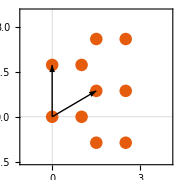

```mathematica
Clear[a,unicell,vasbasis,vas,crystal,pts0,pts1,basisArrows,crystal]
a=Sqrt[3];
unicell={{0,0},{1,0}};
vasbasis={{3/2,Sqrt[3]/2},{0,Sqrt[3]}};
vas={{0,0},{1,0},{0,1},{1,1},{1,-1}}.vasbasis;

crystal=Module[{pts0=Thread[-1{1,-1}->unicell]},<|#->MapAt[TranslationTransform[#],pts0,{All,2}]&/@vas|>];

pts0=Flatten[Values@crystal,1];pts1=Flatten[Values@Values@crystal,1];
basisArrows=Graphics[{Arrowheads[0.02],Arrow[{{0,0},vasbasis[[1]]}],Arrow[{{0,0},vasbasis[[2]]}]}];
Show[ListPlot[pts1,PlotRange->{{-1,4},{-1.5,3.5}},AspectRatio->1,PlotStyle->PointSize[0.05],ImageSize->Small],basisArrows]
```

### Hamiltonian

```mathematica
Clear[params]
params={t->1,λSO->0.06,λR->0.05,λv->0.1,dup->Sqrt[3]+0.01,(*q->1,Ax->1,Ay->-1,ξ1->0.1,ξ2->0.1,*)ω->10,A0->1,mnup->1,angle->0.3}
(hkm=ParallelHMatrixFromHoppings[{crystal[[1]],#},tFunckm[t,λSO,λR,λv]/.params,dup/.params]&/@crystal)//AbsoluteTiming
(hkmflo=ParallelHMatrixFromHoppings[{crystal[[1]],#},tFuncflo[{A0,{2Cos[angle],Sin[angle]}&,ω},mnup][t,λSO,λR,λv]/.params,dup/.params]&/@crystal)//AbsoluteTiming
hBloch2D[{kx_,ky_}]:=HBloch[{kx,ky},hkm];
hBlochflo2D[{kx_,ky_}]:=HBloch[{kx,ky},hkmflo];
```

{t→1,λSO→0.06,λR→0.05,λv→0.1,dup→1.74205,ω→10,A0→1,mnup→1,angle→0.3}

{0.040003,<|{0,0}→SparseArray[…],{3/2,(√3)/2}→SparseArray[…],{0,√3}→SparseArray[…],{3/2,(3 √3)/2}→SparseArray[…],{3/2,-(√3)/2}→SparseArray[…]|>}

{0.123237,<|{0,0}→SparseArray[…],{3/2,(√3)/2}→SparseArray[…],{0,√3}→SparseArray[…],{3/2,(3 √3)/2}→SparseArray[…],{3/2,-(√3)/2}→SparseArray[…]|>}

### Path

```mathematica
Clear[loopfbz]
vbsbasis=ReciprocalVectors[vasbasis];
fig1=FirstBrillouinZonePlot[vbsbasis];
r1=vasbasis[[1]];
r2=vasbasis[[2]];
loopfbz=Module[{Γ,X,Y,Z,n=1000},
{Γ,X,Y,Z}={{0,0},{2/3,1/3},{0.5,0.5},{1/3,2/3}(*,{0,0.5}*)}.Take[vbsbasis,2,2]//N;
PathSample[{Γ,X,Y,Z,Γ},n]
];
fig2=ListPlot[loopfbz[[1]],AspectRatio->Automatic,PlotMarkers->"○"];
Show[fig1,fig2]
```

-Graphics-

### Plot

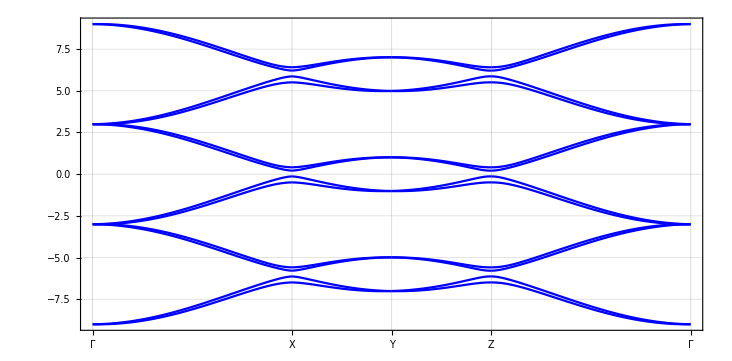

```mathematica
Clear[banddatakm]
banddatakm=ParallelBandData[hBlochflo2D,loopfbz[[1]],Method->"Direct"];
BandPlot[banddatakm,{"Γ","X","Y","Z","Γ"},loopfbz[[2]],FrameTicksStyle->Black,AspectRatio->1/GoldenRatio 0.8,PlotRange->All(*{-2,2}*)]
```

### Test

{t→1,λSO→0.06,λR→0.05,λv→0.1,A0→0.5,ω→7,angle→0.01,dup→1.74205,mnup→1}

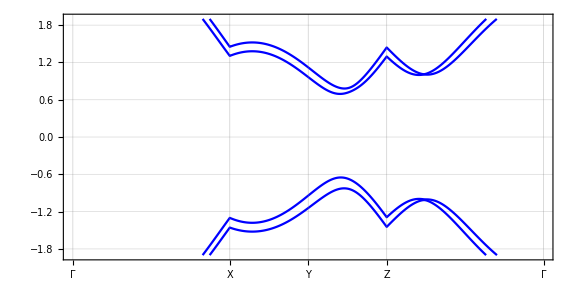

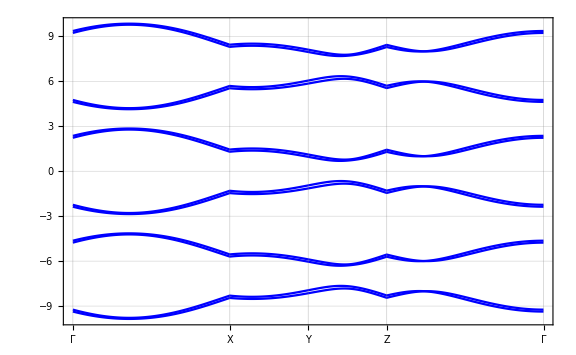

```mathematica
Clear[params]
params={t->1,λSO->0.06,λR->0.05,λv->0.1,A0->0.5,ω->7,angle->0.01,dup->Sqrt[3]+0.01,mnup->1}
(hkmflo=ParallelHMatrixFromHoppings[{crystal[[1]],#},tFuncflo[{A0,{2Cos[angle],Sin[angle]}&,ω},mnup][t,λSO,λR,λv]/.params,dup/.params]&/@crystal)//AbsoluteTiming;
hBlochflo2D[{kx_,ky_}]:=HBloch[{kx,ky},hkmflo];
Clear[banddatakm]
banddatakm=ParallelBandData[hBlochflo2D,loopfbz[[1]],Method->"Direct"];
BandPlot[banddatakm,{"Γ","X","Y","Z","Γ"},loopfbz[[2]],FrameTicksStyle->Black,AspectRatio->1/GoldenRatio 0.8,PlotRange->1.9{-1,1}(*All*),ImageSize->Large]
BandPlot[banddatakm,{"Γ","X","Y","Z","Γ"},loopfbz[[2]],FrameTicksStyle->Black,AspectRatio->1/GoldenRatio (*0.8*),PlotRange->(*1.9{-1,1}*)All,ImageSize->Large]
```

## Zigzag Edge

### a. Lattice

```mathematica
crystStruct1Dy[n_]:=Module[{basis0,atombasis,vRs={{0,0},{0,1},{0,-1}},centerize=TranslationTransform[-Mean[#]][#]&},basis0=Thread[-1{-1,1,-1,1}->{{0,0},{1/2,Sqrt[3]/2},{3/2,Sqrt[3]/2},{2,0}}];
atombasis=Join@@CrystalStructure[vasbasisedge,basis0,Tuples[{Range[-n,n],{0}}]];
CrystalStructure[vasbasis,Nest[Delete[{{-1},{-4}}],atombasis,1 0],vRs]]
```

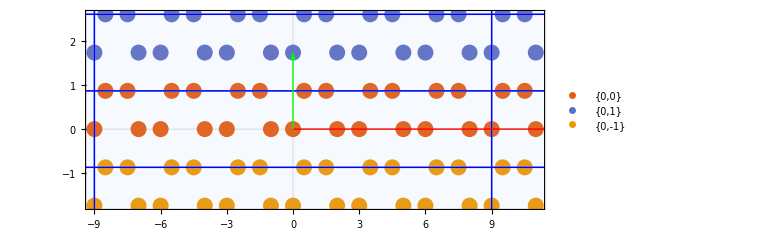

```mathematica
n=3;
vasbasisedge={{3,0},{0,√3}};
CrystalStructurePlot[{2 n,1} vasbasisedge,crystStruct1Dy[n],AspectRatio->Automatic,PlotStyle->PointSize[0.02],PlotRange->All,PlotRangePadding->{Scaled[.1],Scaled[.1]},ImageSize->Large](*For check use*)
```

```mathematica
Clear[cryststruct1dy,n]
n=(*50*)20(*4*);
cryststruct1dy=crystStruct1Dy[n];
```

### b. Hamiltonian

```mathematica
hkmfloedge=ParallelHMatrixFromHoppings[{cryststruct1dy[[1]],#},(*tFunckm[t,λSO,λR,λv]/.params*)tFuncflo[{A0,{2Cos[angle],Sin[angle]}&,ω},mnup][t,λSO,λR,λv]/.params,dup/. params]&/@cryststruct1dy
hBloch1Dy[ky_]:=HBlochFull[{0,ky},hkmfloedge]
(*!这里注意"hBloch1Dy[ky_] := HBlochFull[{0, ky}, h01km]"中是"HBlochFull"而不是"HBloch"
！当晶格周围被完全包围之后使用HBlochFull
！当晶格周围没有被完全包围使用HBloch，会自动补全。*)
```

<|{0,0}→SparseArray[…],{0,√3}→SparseArray[…],{0,-√3}→SparseArray[…]|>

### e. Plot(Quick Check)

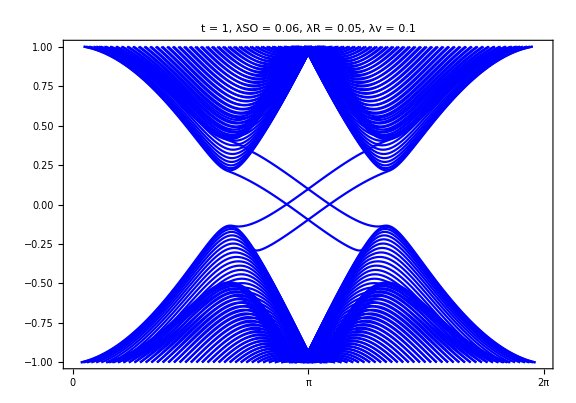

```mathematica
Clear[t,t2,λSO,λv,λR,dup]
params2={t->1,λSO->0.06,λR->0.05,λv->0.1,dup->Sqrt[3]+0.01};
hkmedge=ParallelHMatrixFromHoppings[{cryststruct1dy[[1]],#},tFuncflo[{A0,{2Cos[angle],Sin[angle]}&,ω},mnup][t,λSO,λR,λv]/.params,dup/. params]&/@cryststruct1dy;
eup = 0.25 4; kn = 200 4; kgrid =  Subdivide[##, kn] & @@ ({-2, 0} π/√3);
hBloch1Dy[ky_]:=HBlochFull[{0,ky},hkmedge]
(banddata1dy = 
    ParallelBandData[hBloch1Dy, kgrid, 
     Method ->(*"Direct"*)"Banded"];) // AbsoluteTiming;
BandPlot[Select[AnyTrue[Between[{-1, 1} eup]]][banddata1dy], {"0", "π", "2π"},  Insert[MinMax[kgrid], Mean[kgrid], 2], DataRange -> MinMax[kgrid], AspectRatio ->0.7, PlotRange ->{-1, 1} eup,PlotStyle -> Directive[Blue],ImageSize->Large,PlotLabel->Style[Row[{"t = ",t/.params2,", λSO = ",λSO/.params2,", λR = ",λR/.params2,", λv = ",λv/.params2}],22,FontFamily->"Times New Roman",Italic]]
```